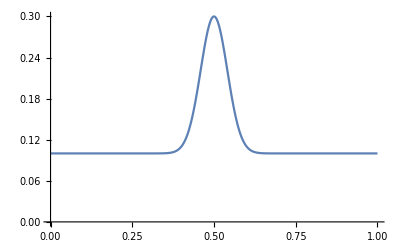

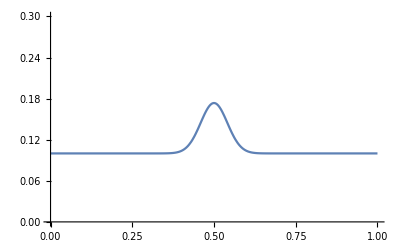

```mathematica
t0 = 0;
t1 = 0.1;
q[t_,x_]:=2/10*E^(-10t)*E^(-300(x-1/2)^2)+1/10
Plot[q[t0,x],{x,0,1},PlotRange->{{0, 1},{0, 0.3}}]
Plot[q[t1,x],{x,0,1},PlotRange->{{0, 1},{0, 0.3}}]
(*D[q[t,x],t]+D[q[t,x]^2-q[t,x]^3,x]+D[q[t,x]^3 D[q[t,x],{x,3}],x]//FullSimplify
D[q[t,x],t]+D[q[t,x]^2-q[t,x]^3,x]//FullSimplify*)
```

```mathematica
D[q[t, x], t] + D[q[t,x]^2-q[t,x]^3,x]//Simplify
```

1/5 ⅇ^(-30 (t+30 (-1/2+x)^2)) (-36+ⅇ^(20 (t+30 (-1/2+x)^2)) (41-102 x)+72 x-84 ⅇ^(10 (t+30 (-1/2+x)^2)) (-1+2 x))

```mathematica
D[q[t,x],t]
```

-2 ⅇ^(-10 t-300 (-1/2+x)^2)

```mathematica
D[q[t,x]^3 D[q[t,x],{x,3}],x]
```

1/5 (1/10+1/5 ⅇ^(-100 (-1/2+x)^2))^3 (120000 ⅇ^(-100 (-1/2+x)^2)-48000000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)^2+1600000000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)^4)-24 ⅇ^(-100 (-1/2+x)^2) (1/10+1/5 ⅇ^(-100 (-1/2+x)^2))^2 (120000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)-8000000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)^3) (-1/2+x)

```mathematica
D[q[t,x],t]+D[q[t,x]^3 D[q[t,x],{x,3}],x]
```

```mathematica
-2 ⅇ^(-10 t-300 (-1/2+x)^2)+1/5 (1/10+1/5 ⅇ^(-10 t-300 (-1/2+x)^2))^3 (1080000 ⅇ^(-10 t-300 (-1/2+x)^2)-1296000000 ⅇ^(-10 t-300 (-1/2+x)^2) (-1/2+x)^2+129600000000 ⅇ^(-10 t-300 (-1/2+x)^2) (-1/2+x)^4)-72 ⅇ^(-10 t-300 (-1/2+x)^2) (1/10+1/5 ⅇ^(-10 t-300 (-1/2+x)^2))^2 (1080000 ⅇ^(-10 t-300 (-1/2+x)^2) (-1/2+x)-216000000 ⅇ^(-10 t-300 (-1/2+x)^2) (-1/2+x)^3) (-1/2+x)vim
```

```mathematica
D[q[t,x],t]+D[q[t,x]^3 D[q[t,x],{x,3}],x]//Simplify
```

2 ⅇ^(-40 (t+30 (-1/2+x)^2)) (648 ⅇ^(20 (t+30 (-1/2+x)^2)) (14551-118200 x+358200 x^2-480000 x^3+240000 x^4)+1296 ⅇ^(10 (t+30 (-1/2+x)^2)) (21901-177600 x+537600 x^2-720000 x^3+360000 x^4)+864 (29251-237000 x+717000 x^2-960000 x^3+480000 x^4)+ⅇ^(30 (t+30 (-1/2+x)^2)) (777707-6350400 x+19310400 x^2-25920000 x^3+12960000 x^4))

```mathematica
D[q[t,x],t] +D[q[t,x]^2-q[t,x]^3,x]+D[q[t,x]^3 D[q[t,x],{x,3}],x]//Simplify
```

1/5 ⅇ^(-40 (t+30 (-1/2+x)^2)) (8640 (29251-237000 x+717000 x^2-960000 x^3+480000 x^4)+ⅇ^(30 (t+30 (-1/2+x)^2)) (7777121-63504102 x+193104000 x^2-259200000 x^3+129600000 x^4)+12 ⅇ^(20 (t+30 (-1/2+x)^2)) (7857547-63828014 x+193428000 x^2-259200000 x^3+129600000 x^4)+36 ⅇ^(10 (t+30 (-1/2+x)^2)) (7884359-63935998 x+193536000 x^2-259200000 x^3+129600000 x^4))

```mathematica
f[t_,x_]:=ⅇ^(-40 (t+10 (-1/2+x)^2)) (288 ⅇ^(10 (t+10 (-1/2+x)^2)) (2301-19200 x+59200 x^2-80000 x^3+40000 x^4)+48 ⅇ^(20 (t+10 (-1/2+x)^2)) (4553-38200 x+118200 x^2-160000 x^3+80000 x^4)+2 ⅇ^(30 (t+10 (-1/2+x)^2)) (8811-75200 x+235200 x^2-320000 x^3+160000 x^4)+64 (9253-77000 x+237000 x^2-320000 x^3+160000 x^4))
```

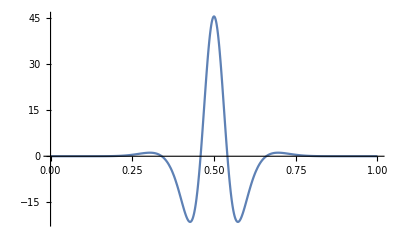

```mathematica
Plot[f[.1,x],{x,0,1},PlotRange->All]
```

```mathematica
NDSolve[{D[u[t,x],t]+D[u[t,x]^2-u[t,x]^3,x]==-27/10 ⅇ^(-225 (1-2 x)^2) (-9+20 ⅇ^(75 (1-2 x)^2)) (-1+2 x),u[0,x]==3/10*E^(-300(x-1/2)^2),u[t,0]==u[t,1]},u,{x,0,1},{t,0,0.5}]
```

{{u→InterpolatingFunction[{{0., 0.5}, {…, 0., 1., …}}, <>]}}

```mathematica
Plot3D[Evaluate[u[t,x]/.%],{t,0,0.5},{x,0,1},PlotRange->All]
```

-Graphics3D-

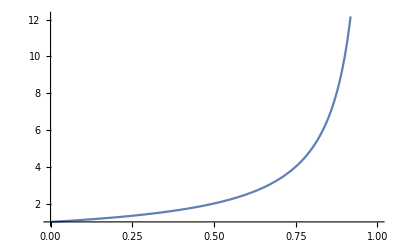

```mathematica
Plot[1/(1 - x),{x,0,1}]
```

```mathematica
Series[1/(1-x),{x,0,2}]
```

1+x+x^2+O[x]^3

```mathematica
Series[(1+1/4 x)/(1-1/4 x),{x,0,2}]
```

```mathematica
(1+1/4 x)/(1-1/4 x)
```

1+x/2+x^2/8+O[x]^3

```mathematica
(4*tn+dt - tn)/(3 - dt)//Simplify
```

(dt+3 tn)/(3-dt)

```mathematica
Series[(dt+3 tn)/(3-dt),{dt,0,2}]
```

tn+1/3 (1+tn) dt+1/9 (1+tn) dt^2+O[dt]^3